# Scaffold protein titration motif

## The model description

This particular motif describe one phosphorylation-desphosphorylation cycle (can be generalized to any futile cycles) with both kinase (K) and phosphatase (P) can be titrated by a scaffold protein (T).

K + S ⇌ KS → K + S_p
P + S_p ⇌ PS_p → P + S
T + K ⇌ TK
T + P ⇌ TP
∅ → T
T → ∅ 

The above reactions show a simple system that composed of one scaffold protein, one kinase, one phosphatase and one substrate. Here we try to descibe this simple system with differential equation following the mass action kinetics.

ⅆ[K]/ⅆt=-k[1][K][S]+k[2][KS]+k[3][KS]-k[7][T][K]+k[8][TK],
ⅆ[P]/ⅆt=-k[4][P][S_p]+k[5][PS_p]+k[6][PS_p]-k[9][T][P]+k[10][TP],
ⅆ[S]/ⅆt=-k[1][K][S]+k[2][KS]+k[6][PS_p],
ⅆ[S_p]/ⅆt=-k[4][P][S_p]+k[3][KS]+k[5][PS_p],
ⅆ[KS]/ⅆt=k[1][K][S]-k[2][KS]-k[3][KS],
ⅆ[PS_p]/ⅆt=k[4][P][S_p]-k[5][PS_p]-k[6][PS_p],
ⅆ[T]/ⅆt=-k[7][T][K]+k[8][TK]-k[9][T][P]+k[10][TP] + k[11]k_d-k_d[T],
ⅆ[TK]/ⅆt=k[7][T][K]-k[8][TK],
ⅆ[TP]/ⅆt=k[9][T][P]-k[10][TP].

And the system need to follow these conservation equations:

[K]+[KS]+[TK]=[K_tot],
[P]+[PS_p]+[TP]=[P_tot],
[S]+[S_p]+[KS]+[PS_p]=[S_tot],
[T]+[TK]+[TP]=[T_tot].

In the following setion, we will solve the differential equations to understand the dynamics and behaviour of such system.

## Understanding the dynamics of the simple system with input pertubations (numerical study)

Since, it is a bit difficult to solve the differential equations analytically. Here we try to study them numerically. By defining two different way to characterising the dynamics with scoring their tempral dynamics when presented with input signal perturbation (the changing of [T]). The quantification can be derived from the actually fitness funcitons for ultrasensitive response and adaptive response. Then we save all the parameter sets as well as their score on ultrasensitivity and adaptation.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t]+k11[t]*kd-kd*x[7][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)
```

```mathematica
AbsoluteTiming[
totK=0.1;totP=0.1;totS=1;
stepNum=5;
sampleSize=100000;

pars={};
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
For[num=1,num≤sampleSize,num++,
Block[{k,T,ssthreshold},k[n_]:=k[n]=10^(RandomReal[]*6-3);
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
totT=1.*^-4;
(*totT=1.*10^(RandomReal[]*4-3);*)

Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]},vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

ks=Array[k,10];
AppendTo[pars,Join[ks,{totT,totK,totP,totS,us,ad,num,(ks[[2]]+ks[[3]])/ks[[1]],(ks[[5]]+ks[[6]])/ks[[4]],ks[[8]]/ks[[7]],ks[[10]]/ks[[9]]}]];
];
];
];
];
]

(*Plot@@{{{(x[7][t]+x[8][t]+x[9][t]),x[4][t]}/.sol},Flatten@{t,x[1]["Domain"]/.sol},PlotLegends->{"T_tot","S_p"}}
ListPlot[Transpose@{xT,x4},PlotRange->{0,10}]*)
(*Print[pars];*)
transPars=Transpose[pars];
Export["saturationSampling.csv",transPars];
(*Export["unsaturationSampling.csv",transPars];*)
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 390.001 and t = 397.971.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 55.8819 and t = 57.3088.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 2932.9 and t = 2977.05.

General::stop: Further output of NDSolve :: evcvmit will be suppressed during this calculation.

{23453.1,Null}

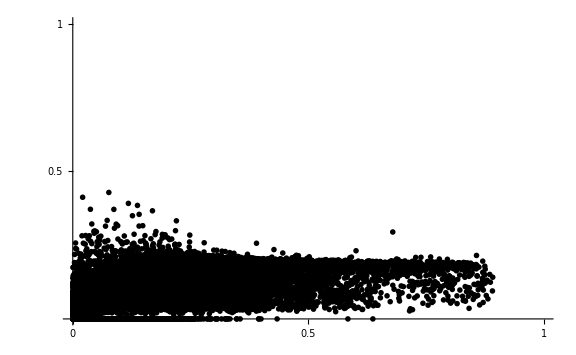

```mathematica
ListPlot[Transpose[{transPars[[15]],transPars[[16]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
```

```mathematica
maxAndIndex[transPars[[15]]]
```

{0.892077,73100}

```mathematica
maxAndIndex[transPars[[16]]]
```

{0.42826,45204}

```mathematica
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
pars[[usIndex]]
```

{4.21408,0.35135,721.263,321.063,0.0741563,0.00544426,94.1622,0.0121232,312.762,64.2999,0.0001,0.1,0.1,1,0.892077,0.141251,73100,171.239,0.000247928,0.000128748,0.205587}

```mathematica
pars[[adIndex]]
```

{857.448,176.296,21.452,279.959,75.2845,57.479,3.36417,0.0153426,595.321,6.53196,0.0001,0.1,0.1,1,0.0766156,0.42826,45204,0.230624,0.474225,0.0045606,0.0109722}

{a→0.893328,b→0.000187849,hillK→475019.,n→3.30405}

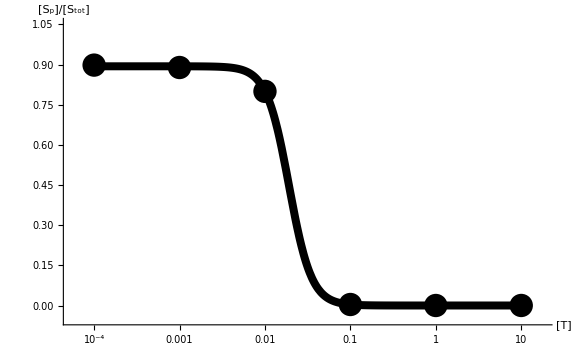

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
stepNum=5;
maxPars=Solve[Array[k,10]==pars[[usIndex]][[Range[10]]]];totT=pars[[usIndex]][[11]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[T]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}], PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

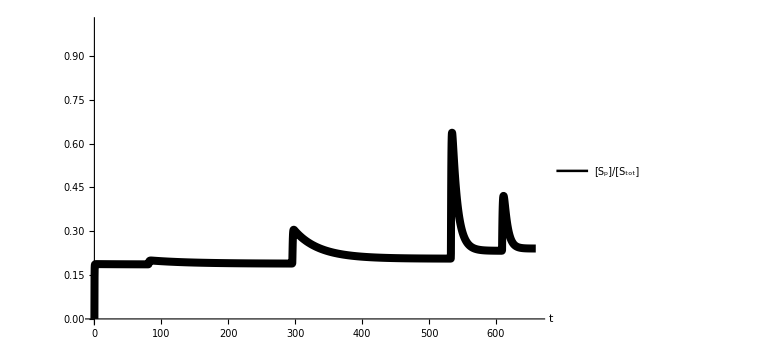

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=pars[[adIndex]][[11]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

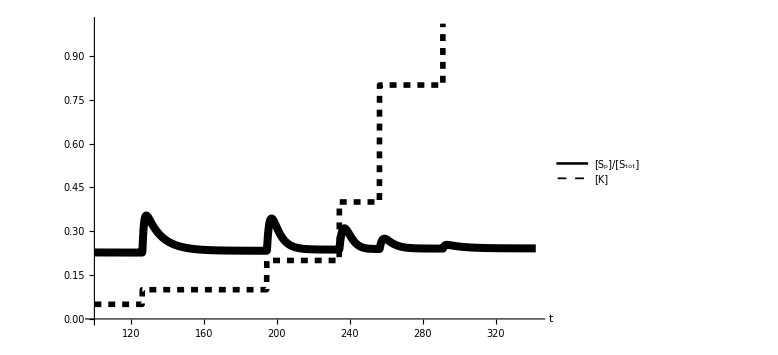

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.05};
stepNum=5;
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=0.05;
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->2*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,100,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.45,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,100,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.15,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

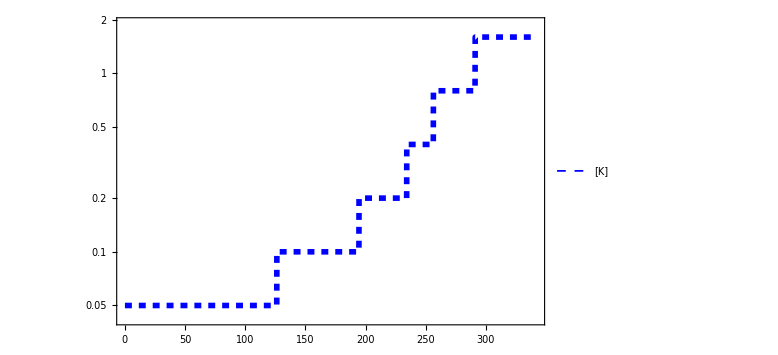

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.15,0.95}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

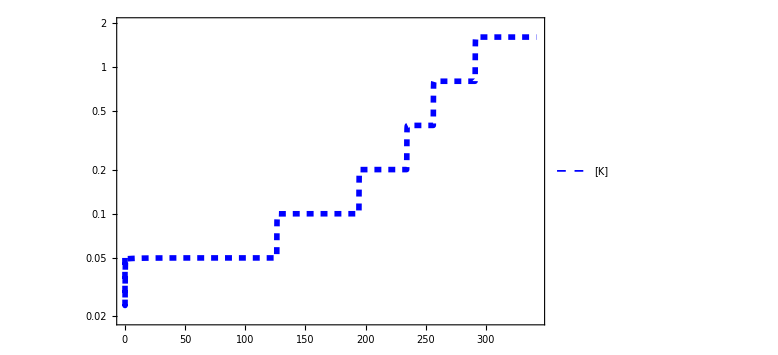

```mathematica
actualInput=LogPlot[{{x[7][t]}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.15,0.95}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

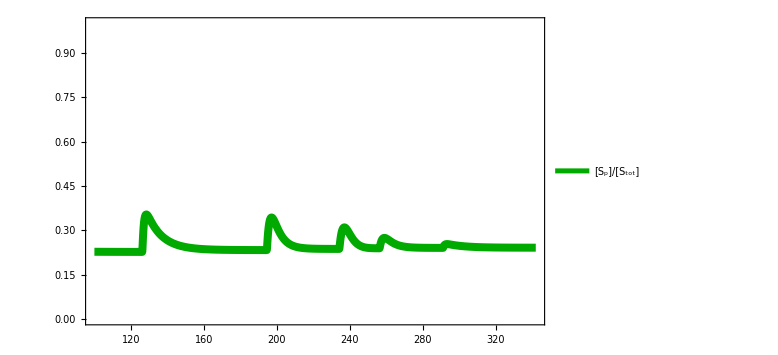

```mathematica
output=Plot[{{x[4][t]/totS}/.sol},{t,100,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.45,0.95}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}]
```

```mathematica
adPlot=Overlay[{output,input}]
Export["scaffoldTitrationVaringTAd.eps",adPlot];
Export["scaffoldTitrationVaringTAd.pdf",adPlot];
```

-Graphics--Graphics-

```mathematica
us1000index=Reverse[Ordering[transPars[[15]],-1000]];
ad1000index=Reverse[Ordering[transPars[[16]],-1000]];
us1000pars=pars[[us1000index]];
ad1000pars=pars[[ad1000index]];
```

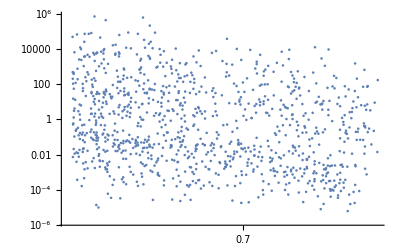

```mathematica
ListLogLogPlot[Transpose[{Transpose[us1000pars][[15]],Transpose[us1000pars][[18]]}]]
```

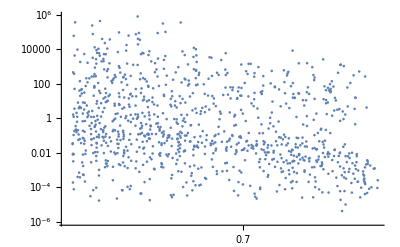

```mathematica
ListLogLogPlot[Transpose[{Transpose[us1000pars][[15]],Transpose[us1000pars][[19]]}]]
```

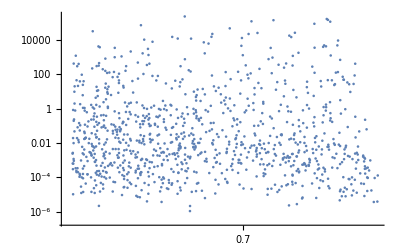

```mathematica
ListLogLogPlot[Transpose[{Transpose[us1000pars][[15]],Transpose[us1000pars][[20]]}]]
```

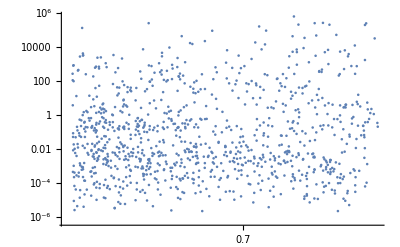

```mathematica
ListLogLogPlot[Transpose[{Transpose[us1000pars][[15]],Transpose[us1000pars][[21]]}]]
```

## Past

```mathematica
us10index=Reverse[Ordering[transPars[[15]],-10]]
```

{40183,48555,65143,60335,24361,84488,89197,41864,21182,16345}

```mathematica
ad10index=Reverse[Ordering[transPars[[16]],-10]]
```

{46757,51362,47620,36386,59792,93994,85192,78829,3938,62006}

```mathematica
us10pars=pars[[us10index]]
```

{{0.0152058,550.394,26.7347,0.0255653,120.706,0.576381,60.5834,41.0397,746.636,0.00360504,8.25277,0.0001,0.1,1,0.948424,0.0566003,40686,37954.4,4744.02,0.677409,4.82838×10^-6},{0.00473897,8.82369,1.52798,0.0184661,39.6837,0.23236,0.0444855,0.24809,8.27808,0.00426559,5.35996,0.0001,0.1,1,0.94798,0.0648051,49163,2184.37,2161.58,5.57688,0.000515287},{0.0164457,1.18513,0.0529798,0.0542984,120.86,0.00232731,21.4329,0.00128623,119.347,121.77,0.00214021,0.0001,0.1,1,0.947482,0.0754808,65957,75.2847,2225.89,0.0000600119,1.02031},{0.0326832,36.1596,0.79838,0.00168478,49.0116,0.0505784,0.0144578,0.00450823,9.17493,0.343141,0.00100142,0.0001,0.1,1,0.947433,0.,61082,1130.79,29120.8,0.311821,0.0373999},{0.00650093,0.165867,0.0197379,0.00896958,29.8697,0.00162253,193.383,6.67945,1.19466,27.9724,3.42216,0.0001,0.1,1,0.946644,0.0792925,24669,28.5506,3330.29,0.0345399,23.4146},{0.00121122,7.20633,10.2176,0.00128656,138.905,0.00100868,33.5046,0.724779,0.0601076,0.100309,0.0669181,0.0001,0.1,1,0.946559,0.0827331,85545,14385.4,107967.,0.0216322,1.66883},{0.00310479,8.555,2.38629,0.0792271,696.826,0.0182071,0.186621,1.48953,0.365057,0.0141316,3.24321,0.0001,0.1,1,0.946308,0.0457594,90312,3524.,8795.52,7.98156,0.0387108},{0.002841,5.30295,1.68763,0.00259356,2.77253,0.0119474,355.789,5.56973,342.319,0.0902507,8.58838,0.0001,0.1,1,0.946158,0.106927,42393,2460.6,1073.61,0.0156546,0.000263645},{0.00222896,0.0411426,0.0186165,0.0133868,0.00681763,27.2137,77.6616,15.9762,11.0276,0.00113207,1.19513,0.0001,0.1,1,0.946042,0.0469308,21454,26.8103,2033.39,0.205716,0.000102659},{0.0591693,726.422,8.51065,0.0528938,2.51538,1.10805,0.00189412,0.397784,31.1658,0.00754719,1.88783,0.0001,0.1,1,0.945457,0.,16550,12420.8,68.5038,210.01,0.000242162}}

```mathematica
ad10pars=pars[[ad10index]]
```

{{29.7712,0.00985813,2.01657,111.111,8.04903,436.845,146.073,0.00268851,48.0433,0.00798703,0.851575,0.0001,0.1,1,0.0182966,0.581416,47351,0.0680666,4.00404,0.0000184052,0.000166246},{6.49517,0.303449,2.04666,728.946,0.137888,58.9909,380.194,0.0236047,347.476,0.00551541,0.142476,0.0001,0.1,1,0.0323854,0.485492,51998,0.361823,0.0811154,0.000062086,0.0000158728},{160.03,87.4493,1.31851,866.858,0.0115362,16.5213,639.492,1.81817,76.588,0.01788,0.399806,0.0001,0.1,1,0.0250654,0.463515,48218,0.554694,0.0190721,0.00284314,0.000233457},{3.06621,5.49841,0.608677,18.998,3.75117,559.66,0.541876,0.00209936,81.4101,0.0544977,0.439828,0.0001,0.1,1,0.0971121,0.457968,36849,1.99174,29.6563,0.00387424,0.000669422},{0.657368,0.00780015,1.62712,225.204,0.0308949,612.298,273.423,0.0272757,129.064,0.00582289,1.3239,0.0001,0.1,1,0.00403979,0.440562,60533,2.48707,2.71899,0.0000997563,0.0000451162},{508.348,1.07501,23.0001,868.394,0.03813,178.203,10.0877,0.00116491,116.297,0.018354,0.288408,0.0001,0.1,1,0.0074898,0.434559,95160,0.0473594,0.205253,0.000115478,0.000157821},{346.693,373.612,2.07537,131.715,22.2274,342.617,28.5312,0.169311,1.71511,0.0289849,3.52502,0.0001,0.1,1,0.211489,0.421953,86255,1.08363,2.76996,0.00593424,0.0168998},{412.299,80.0976,1.03157,802.382,0.236617,12.8867,825.285,11.9355,0.196495,0.00396627,1.3959,0.0001,0.1,1,0.0738737,0.416159,79820,0.196773,0.0163555,0.0144623,0.0201851},{26.7072,0.225819,5.08805,81.6347,0.420222,200.634,26.5474,0.00239127,2.87569,0.00299844,5.59746,0.0001,0.1,1,0.0308346,0.392169,3989,0.198968,2.46285,0.0000900756,0.00104268},{0.497824,0.00705563,535.227,531.036,15.759,99.8258,202.577,0.00150214,346.328,0.00117905,2.98006,0.0001,0.1,1,0.00239886,0.392066,62781,1075.15,0.217659,7.41518×10^-6,3.40444×10^-6}}

```mathematica
us10pars={{0.015205846796259167,550.3944579159456,26.734683253024173,0.02556525291577048,120.70562911952993,0.5763814532369987,60.583390059512965,41.039734153889725,746.6358353492825,0.0036050445171060892,8.252769016992334,0.0001,0.1,1,0.9484241151288099,0.056600313684937474,40686,37954.42298622599,4744.017630975655,0.6774090078745199,4.828383994480548*^-6},{0.004738965349510283,8.8236869796789,1.5279766257476195,0.018466134036467758,39.68368520253024,0.2323597806413694,0.04448548753782595,0.24809009830166948,8.278078051889915,0.0042655871122212995,5.359962118760654,0.0001,0.1,1,0.9479796304859169,0.0648051218096276,49163,2184.37208166045,2161.581027428025,5.576877135284149,0.0005152871337384226},{0.01644565466157307,1.1851265833363094,0.05297979627858425,0.05429835558034022,120.86006250472708,0.0023273137638049183,21.43291075002426,0.0012862302702856586,119.34658290442994,121.77000229000696,0.0021402111119947537,0.0001,0.1,1,0.9474817779725958,0.07548081191289957,65957,75.28471228985818,2225.8941090704316,0.000060011926764739724,1.0203057291344289},{0.032683212515265424,36.15959191874634,0.7983801369580218,0.0016847849129702586,49.011639215963385,0.05057835986348977,0.014457750623246763,0.004508230083066135,9.174931224978854,0.34314133494250143,0.0010014222988226833,0.0001,0.1,1,0.947432994629299,0.,61082,1130.7937381749825,29120.760281103587,0.31182098796318336,0.03739988088502454},{0.006500929563330481,0.16586744917815566,0.019737880586168755,0.008969581774178887,29.86965540277324,0.0016225274236899249,193.383411902936,6.67944758042888,1.1946567893743716,27.97243893424012,3.422156207917619,0.0001,0.1,1,0.9466437056951443,0.07929246425591645,24669,28.55058310603157,3330.286593315715,0.034539920020552034,23.41462349943114},{0.001211221150230446,7.206329033039835,10.21758830981165,0.0012865633726968516,138.9049017186285,0.0010086834409078732,33.50456536168622,0.7247788275835284,0.06010758975919648,0.10030920169739072,0.06691812956804268,0.0001,0.1,1,0.946559463106901,0.08273309823227622,85545,14385.413712051199,107966.62904439714,0.02163224085313285,1.6688275490541256},{0.0031047922822037945,8.554996372298755,2.3862888444724955,0.07922714963136784,696.8259720563954,0.018207068881035238,0.1866210357138387,1.4895266723762832,0.36505688117736335,0.01413163619361035,3.2432079581107858,0.0001,0.1,1,0.9463082334389771,0.045759438196808964,90312,3523.99910276931,8795.522524381968,7.981558277601119,0.03871077884639155},{0.0028410021614117143,5.30295138584364,1.6876297079764038,0.0025935567943782055,2.772533157393896,0.011947350586606604,355.7893948933654,5.569733268479994,342.31878589933984,0.0902507323087995,8.588377818846816,0.0001,0.1,1,0.9461580064072542,0.10692697375756753,42393,2460.6039336296644,1073.6146260672383,0.015654579221365813,0.00026364528044142476},{0.002228960725058574,0.04114255243668739,0.018616467882905156,0.013386794878077162,0.006817626527737361,27.21374142906044,77.66161162728369,15.976244871248403,11.027575245074889,0.001132074440999223,1.195130524201076,0.0001,0.1,1,0.946042253433646,0.046930765590486055,21454,26.81026168283973,2033.3888211110066,0.20571611297383516,0.0001026585097666713},{0.05916926592768915,726.4215290520065,8.510648408763648,0.0528937738747802,2.515376660345834,1.1080463183946518,0.0018941176577904977,0.3977843555892241,31.165795863603407,0.0075471859094240435,1.8878270258297327,0.0001,0.1,1,0.9454572968690893,0.,16550,12420.84325262598,68.50377111148308,210.01037287897023,0.00024216246369751566}};
```

```mathematica
ad10pars={{29.771223516456974,0.009858131475031371,2.0165667396519904,111.11103801150924,8.04903091876997,436.8445582345629,146.073447186022,0.002688514490961823,48.0433323427348,0.00798702899308538,0.8515754977830006,0.0001,0.1,1,0.018296626381681017,0.5814155095095006,47351,0.06806656333781015,4.004044936626813,0.000018405223829201803,0.0001662463572698698},{6.495173884982419,0.303449160945173,2.046656949589212,728.9460202285384,0.13788828124791352,58.990866243804476,380.1939606367445,0.023604723551786094,347.4762495743421,0.00551541378465291,0.14247635323531338,0.0001,0.1,1,0.03238542907456618,0.4854917099011639,51998,0.36182343262096456,0.08111540893866792,0.00006208600345006315,0.000015872779194000405},{160.03034406927426,87.449301620148,1.318506106731833,866.858044413187,0.011536227999241073,16.521297742023936,639.4918808287775,1.8181652293159396,76.58798936349945,0.017880003482978923,0.3998064998389062,0.0001,0.1,1,0.025065428099647298,0.46351538620799426,48218,0.5546936004115185,0.019072135370463053,0.0028431404429398047,0.0002334570163229828},{3.0662072436230936,5.498405772437757,0.6086768762945097,18.998039156800637,3.751166306974741,559.6596611356331,0.541876013767302,0.002099359953837825,81.4101093157353,0.054497740559594506,0.4398280506368734,0.0001,0.1,1,0.09711211272666409,0.4579675973141543,36849,1.9917383801872481,29.656262038018085,0.0038742441084305937,0.0006694222746739507},{0.6573680612693418,0.007800154378741568,1.6271234967425947,225.2042231180153,0.030894926755522547,612.2981480907926,273.42300025485804,0.02727566441882747,129.0641856939382,0.00582289091565828,1.3239036432466929,0.0001,0.1,1,0.004039786492959804,0.44056198052763296,60533,2.487074969788444,2.7189944954836176,0.00009975629114377276,0.00004511624107300098},{508.34809264098567,1.07501256317539,23.00005723500125,868.3941190448579,0.03813004807398619,178.20277633292335,10.08774877886925,0.0011649142342412995,116.29668746283134,0.018354008107285328,0.2884080832637301,0.0001,0.1,1,0.007489797193561068,0.4345590934252392,95160,0.047359417978930736,0.20525347013754947,0.00011547811704841806,0.0001578205579858094},{346.692864980111,373.61207555853986,2.0753728910430373,131.7148437558505,22.227364740994528,342.61719296531567,28.531155606642827,0.16931067184335433,1.7151086972078036,0.02898493747593818,3.525020930767023,0.0001,0.1,1,0.21148852611534305,0.42195317556847495,86255,1.083631901311656,2.7699577914133506,0.005934238142248056,0.016899767066149013},{412.2986853332481,80.09761060536826,1.0315731741462781,802.38178394562,0.23661674441727626,12.886722481863494,825.2848270296176,11.935485475998906,0.19649502945974812,0.003966268830067967,1.395895209375592,0.0001,0.1,1,0.07387365423513433,0.4161590141963329,79820,0.19677284130542488,0.01635548000821786,0.014462262100416111,0.02018508478801218},{26.707184999992954,0.2258190821681327,5.088046043380533,81.63471060393847,0.4202223795334992,200.63390138595824,26.547387178742618,0.0023912716615854895,2.875693639704387,0.00299844231512822,5.597462358206743,0.0001,0.1,1,0.030834632271693082,0.39216932488414635,3989,0.19896762333993892,2.46285094021993,0.00009007559371041458,0.0010426848930390413},{0.4978242442556381,0.007055631962913463,535.2274069283023,531.0362033007426,15.75898938332753,99.82584966809318,202.5768288834093,0.0015021432656351697,346.32760348901377,0.0011790525497715357,2.98006482166812,0.0001,0.1,1,0.002398863325044927,0.39206569768232036,62781,1075.1474415645705,0.2176590566386702,7.4151781026235265*^-6,3.4044428971106763*^-6}};
```

Here we sample [T] to explore that the effect of changing [T] on both adaptive level and ultrasensitive level.

```mathematica
(* From ultrasensitive to adaptive *)
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
Block[{points,iPar,num,ts,usToAdPars,maxPars,transPars},
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=1000;
points=10;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==us10pars[[iPar]][[Range[10]]]];
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
ts={};
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,{totT,us,ad,num}];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"saturatedUsToAd"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedUsToAd"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
Block[{points,iPar,num,usToAdPars,maxPars,transPars},
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=1000;
points=10;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==ad10pars[[iPar]][[Range[10]]]];
adToUsPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"saturatedAdToUs"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedAdToUs"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{3027.46,Null}

Here, we alternatively sample k_s of T interacting K and P.

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},
points=10;

For[iPar=1,iPar≤points,iPar++,
totT=us10pars[[iPar]][[11]];
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[us10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"saturatedUsToAdSampleKs"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedUsToAdSampleKs"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,adToUsPars,maxPars,transPars},
points=10;
For[iPar=1,iPar≤points,iPar++,
totT=ad10pars[[iPar]][[11]];
adToUsPars={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[ad10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"saturatedAdToUsSampleKs"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedAdToUsSampleKs"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
```

Now, we finally to sample both [T] and k_s.

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},
points=10;

For[iPar=1,iPar≤points,iPar++,
(*totT=us10pars[[iPar]][[11]];*)
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);
{maxPars}=Solve[Array[k,10]==Join[us10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"saturatedUsToAdSampleAll"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedUsToAdSampleAll"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];

Block[{points,iPar,num,adToUsPars,maxPars,transPars},
points=10;
For[iPar=1,iPar≤points,iPar++,
(*totT=ad10pars[[iPar]][[11]];*)
adToUsPars={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);
{maxPars}=Solve[Array[k,10]==Join[ad10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"saturatedAdToUsSampleAll"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedAdToUsSampleAll"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{4500.84,Null}

Now, we re-sample the [T] to get the new drawings but with colour as [T]

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
Block[{points,iPar,num,adToUsPars,maxPars,transPars},
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=1000;
points=10;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==ad10pars[[iPar]][[Range[10]]]];
adToUsPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"saturatedAdToUsColour"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedAdToUsColour"<>ToString[iPar]<>".eps",vsPlot];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export[NotebookDirectory[]<>"saturatedAdToUsColourLeg"<>ToString[iPar]<>".pdf",pLeg];
Export[NotebookDirectory[]<>"saturatedAdToUsColourLeg"<>ToString[iPar]<>".eps",pLeg];

];
];
]
```

{2944.28,Null}

Here we sample K_1 and K_2 (which are k_(1~6)) from ultrasensitive networks by fixing the [T] and k_(7~10).

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=10000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},
points=10;

For[iPar=1,iPar≤points,iPar++,
totT=us10pars[[iPar]][[11]];
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[Table[1.*10^(RandomReal[]*6-3),{i,1,6}],us10pars[[iPar]][[Range[4]+6]]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,Join[{totT,us,ad,num},{k[1],k[2],k[3],k[4],k[5],k[6],k[7],k[8],k[9],k[10],(k[2]+k[3])/k[1],(k[5]+k[6])/k[4],k[8]/k[7],k[10]/k[9]}/.maxPars]];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"saturatedUsToAdSampleK1K2"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedUsToAdSampleK1K2"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];

Block[{points,iPar,num,adToUsPars,maxPars,transPars},
points=10;
For[iPar=1,iPar≤points,iPar++,
totT=ad10pars[[iPar]][[11]];
adToUsPars={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[Table[1.*10^(RandomReal[]*6-3),{i,1,6}],ad10pars[[iPar]][[Range[4]+6]]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,Join[{totT,us,ad,num},{k[1],k[2],k[3],k[4],k[5],k[6],k[7],k[8],k[9],k[10],(k[2]+k[3])/k[1],(k[5]+k[6])/k[4],k[8]/k[7],k[10]/k[9]}/.maxPars]];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"saturatedAdToUsSampleK1K2"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedAdToUsSampleK1K2"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{55691.4,Null}

## Test the functions

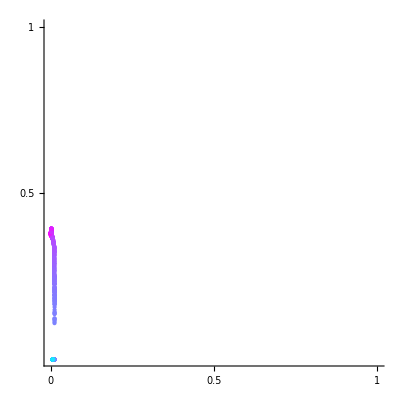
-Graphics- | -Graphics-
-Graphics-

```mathematica
usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude=Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
pl=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
plotLegend[{min_,max_},n_,col_]:=Graphics[{MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]]},Frame->False,FrameTicks->None,PlotRangePadding->.5];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
(*pLeg=Grid[{{Show[pl,ImageSize->{Automatic,600}],Show[leg,ImageSize->{Automatic,150}]}}]*)
Grid[{{Show[pl,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}]
(*Export[NotebookDirectory[]<>"saturatedAdToUsColourLeg"<>ToString[iPar]<>".pdf",pLeg];*)
```

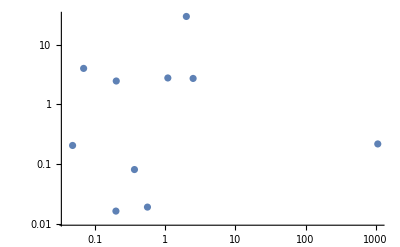

```mathematica
ListLogLogPlot[Transpose[{Transpose[ad10pars][[18]],Transpose[ad10pars][[19]]}]]
```

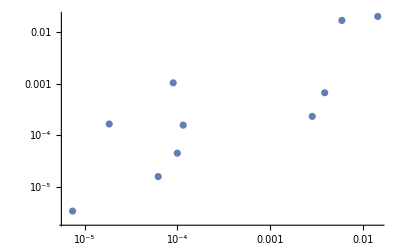

```mathematica
ListLogLogPlot[Transpose[{Transpose[ad10pars][[20]],Transpose[ad10pars][[21]]}]]
```

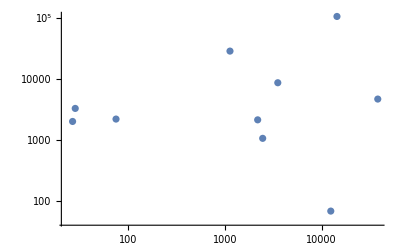

```mathematica
ListLogLogPlot[Transpose[{Transpose[us10pars][[18]],Transpose[us10pars][[19]]}]]
```

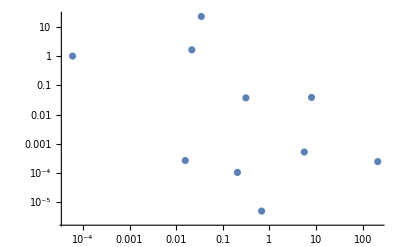

```mathematica
ListLogLogPlot[Transpose[{Transpose[us10pars][[20]],Transpose[us10pars][[21]]}]]
```

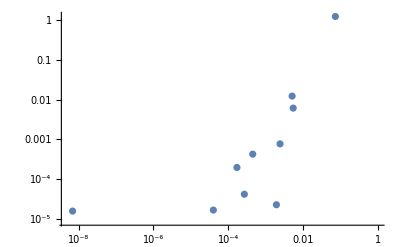

```mathematica
ListLogLogPlot[Transpose[{Transpose[ad10pars][[20]]/Transpose[ad10pars][[18]],Transpose[ad10pars][[21]]/Transpose[ad10pars][[19]]}]]
```

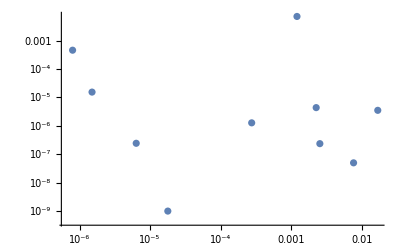

```mathematica
ListLogLogPlot[Transpose[{Transpose[us10pars][[20]]/Transpose[us10pars][[18]],Transpose[us10pars][[21]]/Transpose[us10pars][[19]]}]]
```